```mathematica
ClearAll["Global`*"]
```

```mathematica
R0 = a(T - T/2Sqrt[-Log[1-4a^2](T/K + N)] )+ T N/2
```

(N T)/2+a (T-1/2 T √(-(N+T/K) Log[1-4 a^2]))

```mathematica
R = a(T -T/K - T/2Sqrt[-Log[1-4a^2](T/K + N)] )+ T N/2
```

(N T)/2+a (T-T/K-1/2 T √(-(N+T/K) Log[1-4 a^2]))

```mathematica
R2 = Normal[Series[R0,{a,0,2}]]
```

a T+(N T)/2-a^2 T √((K N+T)/K)

```mathematica
amax = Simplify[Solve[D[R2,a]==0,a]]
```

{{a→1/(2 √(N+T/K))}}

```mathematica
R3 = Simplify[R2 /. a->1/(2 √(N+T/K))]
```

(N T)/2+(K T √(N+T/K))/(4 (K N+T))

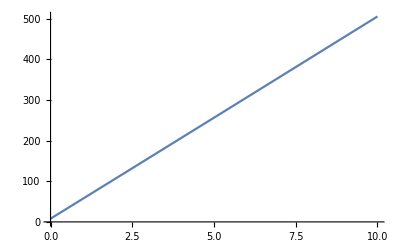

```mathematica
Plot[R3 //. {T-> 100,K->10},{N,0,10}]
```

```mathematica
Nmin = Simplify[Solve[D[R3,N]==0,N]]
```

{{N→1/4 (2^(2/3)-(4 T)/K)}}

```mathematica
Reduce[1/4 (2^(2/3)-(4 T)/K)>0,T]
```

(K<0&&T>K/(2 2^(1/3)))||(K>0&&T<K/(2 2^(1/3)))